```mathematica
(*Code to generate plots for the paper "Geometry of Contraction-Induced Flows."*)
```

```mathematica
(*Returns the location of max(ψTilde] as well as the value qTilde and max(ψTilde)*)
calcψExtremaRadialContractionWaveΩ0Tilde[ΔP_,η_,ν_]:=Module[{uxPrime,uxPrimePrime,ur,urPrime,rs,xsPrime,qTilde,vXTilde,vRTilde,ψ,sols,ψMax,ξ,R,ξ0,R0},
ur[ξ_]:=η Cos[2π ξ];
urPrime[ξ_]:= -2π η Sin[2π ξ];
uxPrime[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
uxPrimePrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
xsPrime[ξ_]:=1+uxPrime[ξ];
qTilde =(-ΔP-NIntegrate[rs[ξ]^(-2) xsPrime[ξ]^2,{ξ,0,1}])/NIntegrate[rs[ξ]^(-4) xsPrime[ξ],{ξ,0,1}];
vXTilde[ξ_,R_]:=2(1+(rs[ξ]^2 xsPrime[ξ])^(-1) qTilde) (1-(R)^2)-1;
vRTilde[ξ_,R_]:=-(2 rs[ξ]urPrime[ξ]xsPrime[ξ]+rs[ξ]^2 uxPrimePrime[ξ])/(rs[ξ]^2 xsPrime[ξ])R/2 (1-R^2);
ψ[ξ_,R_]:=qTilde R^2 (2-R^2) + rs[ξ]^2 xsPrime[ξ] R^2 (1-R^2);
sols=Quiet[NSolve[{vXTilde[ξ,R]==0, vRTilde[ξ,R]==0,0<=ξ<1,0<R<1},{ξ,R}]];
AppendTo[sols,{ξ->0,R->0}];
ψMax=Max[ψ[ξ,R]/.sols];
{ξ0,R0}=({ξ,R}/.sols[[Ordering[ψ[ξ,R]/.sols,-1]]])[[1]]; (*location of the max*)
{{ξ0,R0},{qTilde,ψMax}}];
calcψExtremaLongitudinalContractionWaveΩ0Tilde[ΔP_,η_,ν_]:=Module[{uxPrime,uxPrimePrime,ur,urPrime,rs,xsPrime,qTilde,vXTilde,vRTilde,ψ,sols,ψMax,ξ,R,ξ0,R0},
uxPrime[ξ_]:=η Cos[2π ξ];
uxPrimePrime[ξ_]:= -2π η Sin[2π ξ];
ur[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
urPrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
xsPrime[ξ_]:=1+uxPrime[ξ];
qTilde =(-ΔP-NIntegrate[rs[ξ]^(-2) xsPrime[ξ]^2,{ξ,0,1}])/NIntegrate[rs[ξ]^(-4) xsPrime[ξ],{ξ,0,1}];
vXTilde[ξ_,R_]:=2(1+(rs[ξ]^2 xsPrime[ξ])^(-1) qTilde) (1-(R)^2)-1;
vRTilde[ξ_,R_]:=-(2 rs[ξ]urPrime[ξ]xsPrime[ξ]+rs[ξ]^2 uxPrimePrime[ξ])/(rs[ξ]^2 xsPrime[ξ])R/2 (1-R^2);
ψ[ξ_,R_]:=qTilde R^2 (2-R^2) + rs[ξ]^2 xsPrime[ξ] R^2 (1-R^2);
sols=Quiet[NSolve[{vXTilde[ξ,R]==0, vRTilde[ξ,R]==0,0<=ξ<1,0<R<1},{ξ,R}]];
AppendTo[sols,{ξ->0,R->0}];
ψMax=Max[ψ[ξ,R]/.sols];
{ξ0,R0}=({ξ,R}/.sols[[Ordering[ψ[ξ,R]/.sols,-1]]])[[1]]; (*location of the max*)
{{ξ0,R0},{qTilde,ψMax}}];

(* Plots v vector field (Lagrangian) with optional particle trajectories starting at particlePositions at t=0. *)
(* Only the first 4 parameters are physical. The rest are for visualization purposes. *)
plotvRadialContractionWaveΩ0[t_,ΔP_,η_,ν_,nRGridlines_,nXGridlines_,nRPoints_,nXPoints_,room_,vMinLength_,vMaxLength_,vMaxVal_,arrowheadSize_,particlePositions_]:=
Module[{ls,lsDot,ux,uxPrime,uxPrimePrime,ur,urPrime,rs,rsDot,q,rm4l,rm2l2,vX,vR,vNorm,vScaled,lst,lsDott,rst,rsDott,qt,vXt,vRt,gridlines,points,arrows,solFunc,initialPositionPoints,trajectories,finalPositionPoints,metric,Xp0,Rp0,Xp,Rp,tt,X1=-.5, X2=.5},
(*Uniform sinusoidal stretching dynamics*)
(*Will need the t parameter only for plotting particle trajectories.*)
ur[ξ_]:=η Cos[2π ξ];
urPrime[ξ_]:=-2π η Sin[2π ξ];
uxPrime[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
uxPrimePrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
rsDot[ξ_]:=-urPrime[ξ];
ls[ξ_]:=1+uxPrime[ξ];
lsDot[ξ_]:=-uxPrimePrime[ξ];
rm4l = NIntegrate[rs[ξ]^(-4) ls[ξ],{ξ,0,1}];
rm2l2 = NIntegrate[rs[ξ]^(-2) ls[ξ]^2,{ξ,0,1}];
q[ξ_]:=rs[ξ]^2 ls[ξ] - rm2l2/rm4l - ΔP/rm4l;
vX[R_,ξ_]:=2 q[ξ]/(rs[ξ]^2 ls[ξ]) (1 - R^2);
vR[R_,ξ_]:= 1/(rs[ξ]^2 ls[ξ])(2 rs[ξ] rsDot[ξ] ls[ξ] + rs[ξ]^2 lsDot[ξ])R/2 (1-R^2);

lst[X_]:=ls[X-t];
lsDott[X_]:= lsDot[X-t];
rst[X_]:=rs[X-t];
rsDott[X_]:=rsDot[X-t];
qt[X_]:=q[X-t];
vXt[R_,X_]:=vX[R,X-t];
vRt[R_,X_]:= vR[R,X-t];
vNorm[R_,X_]:=Sqrt[vXt[R,X]^2 + vRt[R,X]^2];

(*Now plot it.*)
(*gridlines are in this case the constant spaced X and R gridlines*)
gridlines = ParametricPlot[{Table[{S+X1,RR},{RR,0,1,1/nRGridlines}],Table[{XX,S},{XX,X1,X2,1/nXGridlines}]},{S,0,1},PlotStyle->LightGray,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None];

(*points where the velocity will be plotted.*)
(*It's necessary to use Arrow graphics to have more flexibility and put the base of an arrow at a point as opposed to VectorPlot which puts the center of an arrow at the point.*)
points = Flatten[Table[{X,R},{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];

(*velocities to be plotted, scaled to be the length of the arrows. *)
(*The lowercase 'v' denotes motion in the undeformed material frame.*)
(*vMaxVal and vMaxLength are defined such that when |v| = vMaxVal, the vector is length vMaxLength.*)
(*vMaxVal should be chosen to be about the maximum value of |v| over ALL times.*)
(*To avoid tiny arrows, can include a threshold: a minimum arrow length vMinLength.*)
vScaled = Flatten[Table[{vXt[R,X],vRt[R,X]}*vMaxLength/vMaxVal HeavisideTheta[vNorm[R,X]*vMaxLength/vMaxVal-vMinLength],{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];
arrows=Graphics[{Blue,Arrowheads[arrowheadSize], Table[Arrow[{points[[j]],points[[j]]+vScaled[[j]]}],{j,1,Length[points]}]}];

(*Particle trajectories.*)
solFunc=ParametricNDSolveValue[{Xp'[tt]==vX[Rp[tt],Xp[tt]-tt],Rp'[tt]==vR[Rp[tt],Xp[tt]-tt],Xp[0]==Xp0,Rp[0]==Rp0},{Xp[tt],Rp[tt]},{tt,0,t},{Xp0,Rp0}];
initialPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[particlePositions[[j]]],White,PointSize[.015],Point[particlePositions[[j]]]}],{j,1,Length[particlePositions]}];
trajectories = Table[ParametricPlot[solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]],{tt,0,t},PlotStyle->Red,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None],{j,1,Length[particlePositions]}];
finalPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]]/.tt->t]}],{j,1,Length[particlePositions]}];

(*Finally, display the gridlines, arrow graphics (velocity field), and particle trajectories.*)
Show[gridlines,arrows,initialPositionPoints,trajectories,finalPositionPoints,ImageSize->Large]
];

(*Same but with the V velocity field (Eulerian) *)
plotvRadialContractionWaveΩ[t_,ΔP_,η_,ν_,nRGridlines_,nXGridlines_,nRPoints_,nXPoints_,room_,vMinLength_,vMaxLength_,vMaxVal_,arrowheadSize_,particlePositions_]:=
Module[{ls,lsDot,xs,rs,rsDot,q,rm4l,rm2l2,vX,vR,vNorm,VScaled,lst,lsDott,rst,rsDott,qt,vXt,vRt,Vxt,Vrt,Vx,Vr,xΣ,xΣt,xΣ0,gridlines,points,arrows,solFunc,initialPositionPoints,trajectories,finalPositionPoints,xp0,rp0,xp,rp,ur,urPrime,uxPrime,uxPrimePrime,Xp0,Rp0,Xp,Rp,tt,X1=-.5, X2=.5},
(*Uniform sinusoidal stretching dynamics*)
(*Will need the t parameter only for plotting particle trajectories.*)

ur[ξ_]:=η Cos[2π ξ];
urPrime[ξ_]:= -2π η Sin[2π ξ];
uxPrime[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
uxPrimePrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
rsDot[ξ_]:=-urPrime[ξ];
ls[ξ_]:=1+uxPrime[ξ];
lsDot[ξ_]:=-uxPrimePrime[ξ];

xs[tt_?NumericQ,X_?NumericQ]:=X+NIntegrate[uxPrime[XX-tt],{XX,0,X}];
rm4l = NIntegrate[rs[ξ]^(-4) ls[ξ],{ξ,0,1}];
rm2l2 = NIntegrate[rs[ξ]^(-2) ls[ξ]^2,{ξ,0,1}];
q[ξ_]:=rs[ξ]^2 ls[ξ] - rm2l2/rm4l - ΔP/rm4l;
vX[R_,ξ_]:=2 q[ξ]/(rs[ξ]^2 ls[ξ]) (1 - R^2);
vR[R_,ξ_]:= 1/(rs[ξ]^2 ls[ξ])(2 rs[ξ] rsDot[ξ] ls[ξ] + rs[ξ]^2 lsDot[ξ])R/2 (1-R^2);
xΣ[tt_,Xvec_]:={xs[tt, Xvec[[1]]],rs[Xvec[[1]]-tt] Xvec[[2]]}; (*We keep xΣ in terms of {X,R} *)
Vx[R_,ξ_]:=ls[ξ] vX[R,ξ]+(1- ls[ξ]);
Vr[R_,ξ_]:=-R rsDot[ξ]vX[R,ξ] +rs[ξ] vR[R,ξ]+R rsDot[ξ];

lst[X_]:=ls[X-t];
lsDott[X_]:= lsDot[X-t];
rst[X_]:=rs[X-t];
rsDott[X_]:=rsDot[X-t];
qt[X_]:=q[X-t];
vXt[R_,X_]:=vX[R,X-t];
vRt[R_,X_]:= vR[R,X-t];
xΣ0[Xvec_]:=xΣ[0,Xvec];
xΣt[Xvec_]:=xΣ[t,Xvec];
Vxt[R_,X_]:=Vx[R,X-t];
Vrt[R_,X_]:= Vr[R,X-t];
vNorm[R_,X_]:=Sqrt[vXt[R,X]^2 + vRt[R,X]^2];

(*Now plot it.*)
(*gridlines are in this case the deformed gridlines*)
gridlines = ParametricPlot[{Table[xΣt[{S+X1,RR}],{RR,0,1,1/nRGridlines}],Table[xΣt[{XX,S}],{XX,X1,X2,1/nXGridlines}]},{S,0,1},PlotStyle->LightGray,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None];

(*points where the velocity will be plotted.*)
(*It's necessary to use Arrow graphics to have more flexibility and put the base of an arrow at a point as opposed to VectorPlot which puts the center of an arrow at the point.*)
points = Flatten[Table[xΣt[{X,R}],{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];

(*velocities to be plotted, scaled to be the length of the arrows. *)
(*The uppercase 'V' denotes motion in the deformed material frame.*)
(*will try using the v normalization even when plotting V*)
VScaled = Flatten[Table[{Vxt[R,X],Vrt[R,X]}*vMaxLength/vMaxVal HeavisideTheta[vNorm[R,X]*vMaxLength/vMaxVal-vMinLength],{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];
arrows=Graphics[{Blue,Arrowheads[arrowheadSize], Table[Arrow[{points[[j]],points[[j]]+VScaled[[j]]}],{j,1,Length[points]}]}];


(*Particle trajectories.*)
solFunc=ParametricNDSolveValue[{Xp'[tt]==vX[Rp[tt],Xp[tt]-tt],Rp'[tt]==vR[Rp[tt],Xp[tt]-tt],Xp[0]==Xp0,Rp[0]==Rp0},{Xp[tt],Rp[tt]},{tt,0,t},{Xp0,Rp0}];
initialPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[xΣ0[particlePositions[[j]]]],White,PointSize[.015],Point[xΣ0[particlePositions[[j]]]]}],{j,1,Length[particlePositions]}];
trajectories = Table[ParametricPlot[xΣ[tt,solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]]],{tt,0,t},PlotStyle->Red,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None],{j,1,Length[particlePositions]}];
finalPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[xΣ[t,solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]]/.tt->t]]}],{j,1,Length[particlePositions]}];

(*Finally, display the gridlines, arrow graphics (velocity field), and particle trajectories.*)
Show[gridlines,arrows,initialPositionPoints,trajectories,finalPositionPoints,ImageSize->Large]
];

(*Same but with co-moving velocity field.*)
plotvRadialContractionWaveΩ0Tilde[t_,ΔP_,η_,ν_,nRGridlines_,nXGridlines_,nRPoints_,nXPoints_,room_,vMinLength_,vMaxLength_,vMaxVal_,arrowheadSize_,particlePositions_]:=
Module[{ls,lsDot,ux,uxPrime,uxPrimePrime,ur,urPrime,rs,rsDot,qTilde,rm4l,rm2l2,vXTilde,vRTilde,vNorm,vScaled,lst,lsDott,rst,rsDott,qt,vXTildet,vRTildet,gridlines,points,arrows,solFunc,initialPositionPoints,trajectories,finalPositionPoints,metric,Xp0,Rp0,Xp,Rp,tt,X1=-.5, X2=.5},
(*Uniform sinusoidal stretching dynamics*)
(*Will need the t parameter only for plotting particle trajectories.*)
ur[ξ_]:=η Cos[2π ξ];
urPrime[ξ_]:=-2π η Sin[2π ξ];
uxPrime[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
uxPrimePrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
rsDot[ξ_]:=-urPrime[ξ];
ls[ξ_]:=1+uxPrime[ξ];
lsDot[ξ_]:=-uxPrimePrime[ξ];
rm4l = NIntegrate[rs[ξ]^(-4) ls[ξ],{ξ,0,1}];
rm2l2 = NIntegrate[rs[ξ]^(-2) ls[ξ]^2,{ξ,0,1}];
qTilde:=- rm2l2/rm4l - ΔP/rm4l;
vXTilde[R_,ξ_]:=2(1+ qTilde/(rs[ξ]^2 ls[ξ])) (1 - R^2)-1;
vRTilde[R_,ξ_]:= 1/(rs[ξ]^2 ls[ξ])(2 rs[ξ] rsDot[ξ] ls[ξ] + rs[ξ]^2 lsDot[ξ])R/2 (1-R^2);
vNorm[R_,ξ_]:=Sqrt[vXTilde[R,ξ]^2 + vRTilde[R,ξ]^2];

(*Now plot it.*)
(*gridlines are in this case the constant spaced X and R gridlines*)
gridlines = ParametricPlot[{Table[{S+X1,RR},{RR,0,1,1/nRGridlines}],Table[{XX,S},{XX,X1,X2,1/nXGridlines}]},{S,0,1},PlotStyle->LightGray,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None];

(*points where the velocity will be plotted.*)
(*It's necessary to use Arrow graphics to have more flexibility and put the base of an arrow at a point as opposed to VectorPlot which puts the center of an arrow at the point.*)
points = Flatten[Table[{X,R},{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];

(*velocities to be plotted, scaled to be the length of the arrows. *)
(*The lowercase 'v' denotes motion in the undeformed material frame.*)
(*vMaxVal and vMaxLength are defined such that when |v| = vMaxVal, the vector is length vMaxLength.*)
(*vMaxVal should be chosen to be about the maximum value of |v| over ALL times.*)
(*To avoid tiny arrows, can include a threshold: a minimum arrow length vMinLength.*)
vScaled = Flatten[Table[{vXTilde[R,ξ],vRTilde[R,ξ]}*vMaxLength/vMaxVal HeavisideTheta[vNorm[R,ξ]*vMaxLength/vMaxVal-vMinLength],{ξ,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];
arrows=Graphics[{Blue,Arrowheads[arrowheadSize], Table[Arrow[{points[[j]],points[[j]]+vScaled[[j]]}],{j,1,Length[points]}]}];

(*Particle trajectories.*)
solFunc=ParametricNDSolveValue[{Xp'[tt]==vXTilde[Rp[tt],Xp[tt]],Rp'[tt]==vRTilde[Rp[tt],Xp[tt]],Xp[0]==Xp0,Rp[0]==Rp0},{Xp[tt],Rp[tt]},{tt,0,t},{Xp0,Rp0}];
initialPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[particlePositions[[j]]],White,PointSize[.015],Point[particlePositions[[j]]]}],{j,1,Length[particlePositions]}];
trajectories = Table[ParametricPlot[solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]],{tt,0,t},PlotStyle->Red,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None],{j,1,Length[particlePositions]}];
finalPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]]/.tt->t]}],{j,1,Length[particlePositions]}];

(*Finally, display the gridlines, arrow graphics (velocity field), and particle trajectories.*)
Show[gridlines,arrows,initialPositionPoints,trajectories,finalPositionPoints,ImageSize->Large]
];

plotvLongitudinalContractionWaveΩ0[t_,ΔP_,η_,ν_,nRGridlines_,nXGridlines_,nRPoints_,nXPoints_,room_,vMinLength_,vMaxLength_,vMaxVal_,arrowheadSize_,particlePositions_]:=
Module[{ls,lsDot,ux,uxPrime,uxPrimePrime,ur,urPrime,rs,rsDot,q,rm4l,rm2l2,vX,vR,vNorm,vScaled,lst,lsDott,rst,rsDott,qt,vXt,vRt,gridlines,points,arrows,solFunc,initialPositionPoints,trajectories,finalPositionPoints,metric,Xp0,Rp0,Xp,Rp,tt,X1=-.5, X2=.5},
(*Uniform sinusoidal stretching dynamics*)
(*Will need the t parameter only for plotting particle trajectories.*)
ux[ξ_]:=η/(2π)Sin[2π ξ];
uxPrime[ξ_]:=η Cos[2π ξ];
uxPrimePrime[ξ_]:=-2π η Sin[2π ξ];
ur[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
urPrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
rsDot[ξ_]:=-urPrime[ξ];
ls[ξ_]:=1+uxPrime[ξ];
lsDot[ξ_]:=-uxPrimePrime[ξ];
rm4l = NIntegrate[rs[ξ]^(-4) ls[ξ],{ξ,0,1}];
rm2l2 = NIntegrate[rs[ξ]^(-2) ls[ξ]^2,{ξ,0,1}];
q[ξ_]:=rs[ξ]^2 ls[ξ] - rm2l2/rm4l - ΔP/rm4l;
vX[R_,ξ_]:=2 q[ξ]/(rs[ξ]^2 ls[ξ]) (1 - R^2);
vR[R_,ξ_]:= 1/(rs[ξ]^2 ls[ξ])(2 rs[ξ] rsDot[ξ] ls[ξ] + rs[ξ]^2 lsDot[ξ])R/2 (1-R^2);

lst[X_]:=ls[X-t];
lsDott[X_]:= lsDot[X-t];
rst[X_]:=rs[X-t];
rsDott[X_]:=rsDot[X-t];
qt[X_]:=q[X-t];
vXt[R_,X_]:=vX[R,X-t];
vRt[R_,X_]:= vR[R,X-t];
vNorm[R_,X_]:=Sqrt[vXt[R,X]^2 + vRt[R,X]^2];

(*Now plot it.*)
(*gridlines are in this case the constant spaced X and R gridlines*)
gridlines = ParametricPlot[{Table[{S+X1,RR},{RR,0,1,1/nRGridlines}],Table[{XX,S},{XX,X1,X2,1/nXGridlines}]},{S,0,1},PlotStyle->LightGray,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None];

(*points where the velocity will be plotted.*)
(*It's necessary to use Arrow graphics to have more flexibility and put the base of an arrow at a point as opposed to VectorPlot which puts the center of an arrow at the point.*)
points = Flatten[Table[{X,R},{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];

(*velocities to be plotted, scaled to be the length of the arrows. *)
(*The lowercase 'v' denotes motion in the undeformed material frame.*)
(*vMaxVal and vMaxLength are defined such that when |v| = vMaxVal, the vector is length vMaxLength.*)
(*vMaxVal should be chosen to be about the maximum value of |v| over ALL times.*)
(*To avoid tiny arrows, can include a threshold: a minimum arrow length vMinLength.*)
vScaled = Flatten[Table[{vXt[R,X],vRt[R,X]}*vMaxLength/vMaxVal HeavisideTheta[vNorm[R,X]*vMaxLength/vMaxVal-vMinLength],{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];
arrows=Graphics[{Blue,Arrowheads[arrowheadSize], Table[Arrow[{points[[j]],points[[j]]+vScaled[[j]]}],{j,1,Length[points]}]}];

(*Particle trajectories.*)
solFunc=ParametricNDSolveValue[{Xp'[tt]==vX[Rp[tt],Xp[tt]-tt],Rp'[tt]==vR[Rp[tt],Xp[tt]-tt],Xp[0]==Xp0,Rp[0]==Rp0},{Xp[tt],Rp[tt]},{tt,0,t},{Xp0,Rp0}];
initialPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[particlePositions[[j]]],White,PointSize[.015],Point[particlePositions[[j]]]}],{j,1,Length[particlePositions]}];
trajectories = Table[ParametricPlot[solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]],{tt,0,t},PlotStyle->Red,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None],{j,1,Length[particlePositions]}];
finalPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]]/.tt->t]}],{j,1,Length[particlePositions]}];

(*Finally, display the gridlines, arrow graphics (velocity field), and particle trajectories.*)
Show[gridlines,arrows,initialPositionPoints,trajectories,finalPositionPoints,ImageSize->Large]
];

plotvLongitudinalContractionWaveΩ[t_,ΔP_,η_,ν_,nRGridlines_,nXGridlines_,nRPoints_,nXPoints_,room_,vMinLength_,vMaxLength_,vMaxVal_,arrowheadSize_,particlePositions_]:=
Module[{ls,lsDot,ux,xs,rs,rsDot,q,rm4l,rm2l2,vX,vR,vNorm,VScaled,lst,lsDott,rst,rsDott,qt,vXt,vRt,Vxt,Vrt,Vx,Vr,xΣ,xΣt,xΣ0,gridlines,points,arrows,solFunc,initialPositionPoints,trajectories,finalPositionPoints,xp0,rp0,xp,rp,ur,urPrime,uxPrime,uxPrimePrime,Xp0,Rp0,Xp,Rp,tt,X1=-.5, X2=.5},
(*Uniform sinusoidal stretching dynamics*)
(*Will need the t parameter only for plotting particle trajectories.*)

ux[ξ_]:=η/(2π)Sin[2π ξ];
uxPrime[ξ_]:=η Cos[2π ξ];
uxPrimePrime[ξ_]:=-2π η Sin[2π ξ];
ur[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
urPrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));

rs[ξ_]:=1+ur[ξ];
rsDot[ξ_]:=-urPrime[ξ];
ls[ξ_]:=1+uxPrime[ξ];
lsDot[ξ_]:=-uxPrimePrime[ξ];

xs[tt_?NumericQ,X_?NumericQ]:=X+ux[X-tt];
rm4l = NIntegrate[rs[ξ]^(-4) ls[ξ],{ξ,0,1}];
rm2l2 = NIntegrate[rs[ξ]^(-2) ls[ξ]^2,{ξ,0,1}];
q[ξ_]:=rs[ξ]^2 ls[ξ] - rm2l2/rm4l - ΔP/rm4l;
vX[R_,ξ_]:=2 q[ξ]/(rs[ξ]^2 ls[ξ]) (1 - R^2);
vR[R_,ξ_]:= 1/(rs[ξ]^2 ls[ξ])(2 rs[ξ] rsDot[ξ] ls[ξ] + rs[ξ]^2 lsDot[ξ])R/2 (1-R^2);
xΣ[tt_,Xvec_]:={xs[tt, Xvec[[1]]],rs[Xvec[[1]]-tt] Xvec[[2]]}; (*We keep xΣ in terms of {X,R} *)
Vx[R_,ξ_]:=ls[ξ] vX[R,ξ]+(1- ls[ξ]);
Vr[R_,ξ_]:=-R rsDot[ξ]vX[R,ξ] +rs[ξ] vR[R,ξ]+R rsDot[ξ];

lst[X_]:=ls[X-t];
lsDott[X_]:= lsDot[X-t];
rst[X_]:=rs[X-t];
rsDott[X_]:=rsDot[X-t];
qt[X_]:=q[X-t];
vXt[R_,X_]:=vX[R,X-t];
vRt[R_,X_]:= vR[R,X-t];
xΣ0[Xvec_]:=xΣ[0,Xvec];
xΣt[Xvec_]:=xΣ[t,Xvec];
Vxt[R_,X_]:=Vx[R,X-t];
Vrt[R_,X_]:= Vr[R,X-t];
vNorm[R_,X_]:=Sqrt[vXt[R,X]^2 + vRt[R,X]^2];

(*Now plot it.*)
(*gridlines are in this case the deformed gridlines*)
(*Note that "room" is now of the form {{left room, right room},{bottom room, top room}}*)
gridlines = ParametricPlot[{Table[xΣt[{S+X1,RR}],{RR,0,1,1/nRGridlines}],Table[xΣt[{XX,S}],{XX,X1,X2,1/nXGridlines}]},{S,0,1},PlotStyle->LightGray,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None];

(*points where the velocity will be plotted.*)
(*It's necessary to use Arrow graphics to have more flexibility and put the base of an arrow at a point as opposed to VectorPlot which puts the center of an arrow at the point.*)
points = Flatten[Table[xΣt[{X,R}],{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];

(*velocities to be plotted, scaled to be the length of the arrows. *)
(*The uppercase 'V' denotes motion in the deformed material frame.*)
(*will try using the v normalization even when plotting V*)
VScaled = Flatten[Table[{Vxt[R,X],Vrt[R,X]}*vMaxLength/vMaxVal HeavisideTheta[vNorm[R,X]*vMaxLength/vMaxVal-vMinLength],{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];
arrows=Graphics[{Blue,Arrowheads[arrowheadSize], Table[Arrow[{points[[j]],points[[j]]+VScaled[[j]]}],{j,1,Length[points]}]}];


(*Particle trajectories.*)
solFunc=ParametricNDSolveValue[{Xp'[tt]==vX[Rp[tt],Xp[tt]-tt],Rp'[tt]==vR[Rp[tt],Xp[tt]-tt],Xp[0]==Xp0,Rp[0]==Rp0},{Xp[tt],Rp[tt]},{tt,0,t},{Xp0,Rp0}];
initialPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[xΣ0[particlePositions[[j]]]],White,PointSize[.015],Point[xΣ0[particlePositions[[j]]]]}],{j,1,Length[particlePositions]}];
trajectories = Table[ParametricPlot[xΣ[tt,solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]]],{tt,0,t},PlotStyle->Red,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None],{j,1,Length[particlePositions]}];
finalPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[xΣ[t,solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]]/.tt->t]]}],{j,1,Length[particlePositions]}];

(*Finally, display the gridlines, arrow graphics (velocity field), and particle trajectories.*)
Show[gridlines,arrows,initialPositionPoints,trajectories,finalPositionPoints,ImageSize->Large]
];

plotvLongitudinalContractionWaveΩ0Tilde[t_,ΔP_,η_,ν_,nRGridlines_,nXGridlines_,nRPoints_,nXPoints_,room_,vMinLength_,vMaxLength_,vMaxVal_,arrowheadSize_,particlePositions_]:=
Module[{ls,lsDot,ux,uxPrime,uxPrimePrime,ur,urPrime,rs,rsDot,qTilde,rm4l,rm2l2,vXTilde,vRTilde,vNorm,vScaled,lst,lsDott,rst,rsDott,qt,vXTildet,vRTildet,gridlines,points,arrows,solFunc,initialPositionPoints,trajectories,finalPositionPoints,metric,Xp0,Rp0,Xp,Rp,tt,X1=-.5, X2=.5},
(*Uniform sinusoidal stretching dynamics*)
(*Will need the t parameter only for plotting particle trajectories.*)
uxPrime[ξ_]:=η Cos[2π ξ];
uxPrimePrime[ξ_]:=-2π η Sin[2π ξ];
ur[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
urPrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
rsDot[ξ_]:=-urPrime[ξ];
ls[ξ_]:=1+uxPrime[ξ];
lsDot[ξ_]:=-uxPrimePrime[ξ];
rm4l = NIntegrate[rs[ξ]^(-4) ls[ξ],{ξ,0,1}];
rm2l2 = NIntegrate[rs[ξ]^(-2) ls[ξ]^2,{ξ,0,1}];
qTilde:=- rm2l2/rm4l - ΔP/rm4l;
vXTilde[R_,ξ_]:=2(1+ qTilde/(rs[ξ]^2 ls[ξ])) (1 - R^2)-1;
vRTilde[R_,ξ_]:= 1/(rs[ξ]^2 ls[ξ])(2 rs[ξ] rsDot[ξ] ls[ξ] + rs[ξ]^2 lsDot[ξ])R/2 (1-R^2);
vNorm[R_,ξ_]:=Sqrt[vXTilde[R,ξ]^2 + vRTilde[R,ξ]^2];

(*Now plot it.*)
(*gridlines are in this case the constant spaced X and R gridlines*)
gridlines = ParametricPlot[{Table[{S+X1,RR},{RR,0,1,1/nRGridlines}],Table[{XX,S},{XX,X1,X2,1/nXGridlines}]},{S,0,1},PlotStyle->LightGray,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None];

(*points where the velocity will be plotted.*)
(*It's necessary to use Arrow graphics to have more flexibility and put the base of an arrow at a point as opposed to VectorPlot which puts the center of an arrow at the point.*)
points = Flatten[Table[{X,R},{X,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];

(*velocities to be plotted, scaled to be the length of the arrows. *)
(*The lowercase 'v' denotes motion in the undeformed material frame.*)
(*vMaxVal and vMaxLength are defined such that when |v| = vMaxVal, the vector is length vMaxLength.*)
(*vMaxVal should be chosen to be about the maximum value of |v| over ALL times.*)
(*To avoid tiny arrows, can include a threshold: a minimum arrow length vMinLength.*)
vScaled = Flatten[Table[{vXTilde[R,ξ],vRTilde[R,ξ]}*vMaxLength/vMaxVal HeavisideTheta[vNorm[R,ξ]*vMaxLength/vMaxVal-vMinLength],{ξ,X1,X2,1/nXPoints},{R,0,1,1/nRPoints}],1];
arrows=Graphics[{Blue,Arrowheads[arrowheadSize], Table[Arrow[{points[[j]],points[[j]]+vScaled[[j]]}],{j,1,Length[points]}]}];

(*Particle trajectories.*)
solFunc=ParametricNDSolveValue[{Xp'[tt]==vXTilde[Rp[tt],Xp[tt]],Rp'[tt]==vRTilde[Rp[tt],Xp[tt]],Xp[0]==Xp0,Rp[0]==Rp0},{Xp[tt],Rp[tt]},{tt,0,t},{Xp0,Rp0}];
initialPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[particlePositions[[j]]],White,PointSize[.015],Point[particlePositions[[j]]]}],{j,1,Length[particlePositions]}];
trajectories = Table[ParametricPlot[solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]],{tt,0,t},PlotStyle->Red,PlotRange->{{X1-room[[1]][[1]],X2+room[[1]][[2]]},{-room[[2]][[1]],1+room[[2]][[2]]}},AspectRatio->nRGridlines/nXGridlines,ImageSize->Large,Axes->None],{j,1,Length[particlePositions]}];
finalPositionPoints = Table[Graphics[{Black,PointSize[.02],Point[solFunc[particlePositions[[j]][[1]],particlePositions[[j]][[2]]]/.tt->t]}],{j,1,Length[particlePositions]}];

(*Finally, display the gridlines, arrow graphics (velocity field), and particle trajectories.*)
Show[gridlines,arrows,initialPositionPoints,trajectories,finalPositionPoints,ImageSize->Large]
];

(*Calculates the ψr such that refluxing (particle speed sp<0) occurs for ψ > ψr. 
If reflux does not occur, ψr = qTilde. 
If all streamlines have negative particle speeds, ψr = 0. *) 
calcψRefluxRadialWave[Δp_,η_,ν_]:=Module[{uxPrime,uxPrimePrime,ur,urPrime,rs,xsPrime,qTilde,vXTilde,vRTilde,ψTilde,Rψ,ξ0=0,R0,ψMax,numR=1000,R,RList,spData,ψR,vpTilde,i,ψr,spList},
{{ξ0,R0},{qTilde,ψMax}}=calcψExtremaRadialContractionWaveΩ0Tilde[Δp,η,ν];
ur[ξ_]:=η Cos[2π ξ];
urPrime[ξ_]:= -2π η Sin[2π ξ];
uxPrime[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
uxPrimePrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
xsPrime[ξ_]:=1+uxPrime[ξ];
vXTilde[ξ_,R_]:=2(1+(rs[ξ]^2 xsPrime[ξ])^(-1) qTilde) (1-(R)^2)-1;
vRTilde[ξ_,R_]:=-(2 rs[ξ]urPrime[ξ]xsPrime[ξ]+rs[ξ]^2 uxPrimePrime[ξ])/(rs[ξ]^2 xsPrime[ξ])R/2 (1-R^2);
ψTilde[ξ_,R_]:=qTilde R^2 (2-R^2) + rs[ξ]^2 xsPrime[ξ] R^2 (1-R^2);
Rψ[ξ_,ψTilde_]:=Sqrt[((2qTilde+rs[ξ]^2xsPrime[ξ])+Sqrt[(2qTilde+rs[ξ]^2xsPrime[ξ])^2-4ψTilde(qTilde+rs[ξ]^2xsPrime[ξ])])/(2(qTilde+rs[ξ]^2 xsPrime[ξ]))];
RList= Table[i/numR ,{i,1,numR}]; 
spData={};
For[i=1,i<numR,i++,(*this line is different than in spplot, we don't want to select the R=R0 solution.*)
R=RList[[i]];
ψR = ψTilde[ξ0,R];
If[ψR*qTilde < 0,
vpTilde=0,
vpTilde=(NIntegrate[1/vXTilde[ξ,Rψ[ξ,ψR]],{ξ,ξ0,ξ0+1}])^(-1)
];
AppendTo[spData,{ψR,1+vpTilde}];
];
spList = Transpose[spData][[2]];
Which[
AllTrue[spList,Positive], ψr = qTilde,
AllTrue[spList,Negative], ψr = 0,
True, ψr = First@MinimalBy[Select[spData,#[[2]]>0&],Last][[1]]
];
ψr
];

calcψRefluxLongitudinalWave[Δp_,η_,ν_]:=Module[{uxPrime,uxPrimePrime,ur,urPrime,rs,xsPrime,qTilde,vXTilde,vRTilde,ψTilde,Rψ,ξ0=0,R0,ψMax,numR=1000,R,RList,spData,ψR,vpTilde,i,ψr,spList},
{{ξ0,R0},{qTilde,ψMax}}=calcψExtremaLongitudinalContractionWaveΩ0Tilde[Δp,η,ν];
uxPrime[ξ_]:=η Cos[2π ξ];
uxPrimePrime[ξ_]:= -2π η Sin[2π ξ];
ur[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
urPrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
xsPrime[ξ_]:=1+uxPrime[ξ];
vXTilde[ξ_,R_]:=2(1+(rs[ξ]^2 xsPrime[ξ])^(-1) qTilde) (1-(R)^2)-1;
vRTilde[ξ_,R_]:=-(2 rs[ξ]urPrime[ξ]xsPrime[ξ]+rs[ξ]^2 uxPrimePrime[ξ])/(rs[ξ]^2 xsPrime[ξ])R/2 (1-R^2);
ψTilde[ξ_,R_]:=qTilde R^2 (2-R^2) + rs[ξ]^2 xsPrime[ξ] R^2 (1-R^2);
Rψ[ξ_,ψTilde_]:=Sqrt[((2qTilde+rs[ξ]^2xsPrime[ξ])+Sqrt[(2qTilde+rs[ξ]^2xsPrime[ξ])^2-4ψTilde(qTilde+rs[ξ]^2xsPrime[ξ])])/(2(qTilde+rs[ξ]^2 xsPrime[ξ]))];
RList= Table[i/numR ,{i,1,numR}]; 
spData={};
For[i=1,i<numR,i++,(*this line is different than in spplot, we don't want to select the R=R0 solution.*)
R=RList[[i]];
ψR = ψTilde[ξ0,R];
If[ψR*qTilde < 0,
vpTilde=0,
vpTilde=(NIntegrate[1/vXTilde[ξ,Rψ[ξ,ψR]],{ξ,ξ0,ξ0+1}])^(-1)
];
AppendTo[spData,{ψR,1+vpTilde}];
];
spList = Transpose[spData][[2]];
Which[
AllTrue[spList,Positive], ψr = qTilde,
AllTrue[spList,Negative], ψr = 0,
True, ψr = First@MinimalBy[Select[spData,#[[2]]>0&],Last][[1]]
];
ψr
];

(*Colors refluxing streamlines red and trapping streamlines blue.*)
(*This function definitely cuases errors in certain cases like negative Δp but it should work for my purposes.*)
plotψRadialWaveΩ0TildeColored[η_,ν_,Δp_,numStreamlines_,aspectRatio_]:=
Module[{ur,urPrime,uxPrime,uxPrimePrime,rs,xsPrime,qTilde,vXTilde,vRTilde,ψ,Rψ,Rψ2,zeros,ξξ,RR,ψMax,numStreamlinesTrapping,numStreamlinesNeither,numStreamlinesReflux,ξMin=-.5, ξMax=.5, RMin=-.01, RMax=1.01,ψr},
ψr =  calcψRefluxRadialWave[Δp,η,ν];
ur[ξ_]:=η Cos[2π ξ];
urPrime[ξ_]:= -2π η Sin[2π ξ];
uxPrime[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
uxPrimePrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
xsPrime[ξ_]:=1+uxPrime[ξ];
qTilde =(-Δp-NIntegrate[rs[ξ]^(-2) xsPrime[ξ]^2,{ξ,0,1}])/NIntegrate[rs[ξ]^(-4) xsPrime[ξ],{ξ,0,1}];
vXTilde[ξ_,R_]:=2(1+(rs[ξ]^2 xsPrime[ξ])^(-1) qTilde) (1-(R)^2)-1;
vRTilde[ξ_,R_]:=-(2 rs[ξ]urPrime[ξ]xsPrime[ξ]+rs[ξ]^2 uxPrimePrime[ξ])/(rs[ξ]^2 xsPrime[ξ])R/2 (1-R^2);
ψ[ξ_,R_]:=qTilde R^2 (2-R^2) + rs[ξ]^2 xsPrime[ξ] R^2 (1-R^2);
Rψ[ξ_,ψ_]:=Sqrt[((2qTilde+rs[ξ]^2xsPrime[ξ])+Sqrt[(2qTilde+rs[ξ]^2xsPrime[ξ])^2-4ψ (qTilde+rs[ξ]^2xsPrime[ξ])])/(2(qTilde+rs[ξ]^2 xsPrime[ξ]))];
Rψ2[ξ_,ψ_]:=Sqrt[((2qTilde+rs[ξ]^2xsPrime[ξ])-Sqrt[(2qTilde+rs[ξ]^2xsPrime[ξ])^2-4ψ (qTilde+rs[ξ]^2xsPrime[ξ])])/(2(qTilde+rs[ξ]^2 xsPrime[ξ]))];
zeros=Quiet[NSolve[{vXTilde[ξξ,RR]==0, vRTilde[ξξ,RR]==0,0<=ξξ<1,0<RR<1},{ξξ,RR}]];
AppendTo[zeros,{ξξ->0,RR->0}];
ψMax=Max[ψ[ξξ,RR]/.zeros];
numStreamlinesTrapping = Max[Floor[numStreamlines*Abs[(ψMax-0)/(ψMax-qTilde)]],2]; 
numStreamlinesNeither = Max[Floor[numStreamlines*Abs[(0-ψr)/(ψMax-qTilde)]],2]; 
numStreamlinesReflux = Max[Floor[numStreamlines*Abs[(ψr-qTilde)/(ψMax-qTilde)]],2]; 
Show[
RegionPlot[Rψ2[ξ,0]<=R<=Rψ[ξ,0],{ξ,-.5,.5},{R,0,1},PlotStyle->RGBColor[55/256,100/256,170/256],BoundaryStyle->None,PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,Frame->False,AspectRatio->aspectRatio],
RegionPlot[Rψ[ξ,0]<=R<=Rψ[ξ,ψr],{ξ,-.5,.5},{R,0,1},PlotStyle->RGBColor[160/256,200/256,225/256],BoundaryStyle->None,PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,Frame->False,AspectRatio->aspectRatio],
RegionPlot[Rψ[ξ,ψr]<=R<=1,{ξ,-.5,.5},{R,0,1},PlotStyle->Lighter[Red],BoundaryStyle->None,PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,Frame->False,AspectRatio->aspectRatio],
ParametricPlot[Table[{{ξ,Rψ[ξ,ψ]},{ξ,Rψ2[ξ,ψ]}},{ψ,0,.99ψMax,.99ψMax/numStreamlinesTrapping}],{ξ,-.5,.5},PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,AspectRatio->aspectRatio],
ParametricPlot[Table[{{ξ,Rψ[ξ,ψ]},{ξ,Rψ2[ξ,ψ]}},{ψ,ψr,0,-ψr/numStreamlinesNeither}],{ξ,-.5,.5},PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,AspectRatio->aspectRatio],
ParametricPlot[Table[{{ξ,Rψ[ξ,ψ]},{ξ,Rψ2[ξ,ψ]}},{ψ,qTilde,ψr,(ψr-qTilde)/numStreamlinesReflux}],{ξ,-.5,.5},PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,AspectRatio->aspectRatio]
]
];

plotψLongitudinalWaveΩ0TildeColored[η_,ν_,Δp_,numStreamlines_,aspectRatio_]:=
Module[{ur,urPrime,uxPrime,uxPrimePrime,rs,xsPrime,qTilde,vXTilde,vRTilde,ψ,Rψ,Rψ2,zeros,ξξ,RR,ψMax,numStreamlinesTrapping,numStreamlinesNeither,numStreamlinesReflux,ξMin=-.5, ξMax=.5, RMin=-.01, RMax=1.01,ψr},
ψr =  calcψRefluxLongitudinalWave[Δp,η,ν];
uxPrime[ξ_]:=η Cos[2π ξ];
uxPrimePrime[ξ_]:= -2π η Sin[2π ξ];
ur[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
urPrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
xsPrime[ξ_]:=1+uxPrime[ξ];
qTilde =(-Δp-NIntegrate[rs[ξ]^(-2) xsPrime[ξ]^2,{ξ,0,1}])/NIntegrate[rs[ξ]^(-4) xsPrime[ξ],{ξ,0,1}];
vXTilde[ξ_,R_]:=2(1+(rs[ξ]^2 xsPrime[ξ])^(-1) qTilde) (1-(R)^2)-1;
vRTilde[ξ_,R_]:=-(2 rs[ξ]urPrime[ξ]xsPrime[ξ]+rs[ξ]^2 uxPrimePrime[ξ])/(rs[ξ]^2 xsPrime[ξ])R/2 (1-R^2);
ψ[ξ_,R_]:=qTilde R^2 (2-R^2) + rs[ξ]^2 xsPrime[ξ] R^2 (1-R^2);
Rψ[ξ_,ψ_]:=Sqrt[((2qTilde+rs[ξ]^2xsPrime[ξ])+Sqrt[(2qTilde+rs[ξ]^2xsPrime[ξ])^2-4ψ (qTilde+rs[ξ]^2xsPrime[ξ])])/(2(qTilde+rs[ξ]^2 xsPrime[ξ]))];
Rψ2[ξ_,ψ_]:=Sqrt[((2qTilde+rs[ξ]^2xsPrime[ξ])-Sqrt[(2qTilde+rs[ξ]^2xsPrime[ξ])^2-4ψ (qTilde+rs[ξ]^2xsPrime[ξ])])/(2(qTilde+rs[ξ]^2 xsPrime[ξ]))];
zeros=Quiet[NSolve[{vXTilde[ξξ,RR]==0, vRTilde[ξξ,RR]==0,0<=ξξ<1,0<RR<1},{ξξ,RR}]];
AppendTo[zeros,{ξξ->0,RR->0}];
ψMax=Max[ψ[ξξ,RR]/.zeros];
numStreamlinesTrapping = Max[Floor[numStreamlines*Abs[(ψMax-0)/(ψMax-qTilde)]],2]; 
numStreamlinesNeither = Max[Floor[numStreamlines*Abs[(0-ψr)/(ψMax-qTilde)]],2]; 
numStreamlinesReflux = Max[Floor[numStreamlines*Abs[(ψr-qTilde)/(ψMax-qTilde)]],2]; 
Show[
RegionPlot[Rψ2[ξ,0]<=R<=Rψ[ξ,0],{ξ,-.5,.5},{R,0,1},PlotStyle->RGBColor[55/256,100/256,170/256],BoundaryStyle->None,PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,Frame->False,AspectRatio->aspectRatio],
RegionPlot[Rψ[ξ,0]<=R<=Rψ[ξ,ψr],{ξ,-.5,.5},{R,0,1},PlotStyle->RGBColor[160/256,200/256,225/256],BoundaryStyle->None,PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,Frame->False,AspectRatio->aspectRatio],
RegionPlot[Rψ[ξ,ψr]<=R<=1,{ξ,-.5,.5},{R,0,1},PlotStyle->Lighter[Red],BoundaryStyle->None,PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,Frame->False,AspectRatio->aspectRatio],
ParametricPlot[Table[{{ξ,Rψ[ξ,ψ]},{ξ,Rψ2[ξ,ψ]}},{ψ,0,.99ψMax,.99ψMax/numStreamlinesTrapping}],{ξ,-.5,.5},PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,AspectRatio->aspectRatio],
ParametricPlot[Table[{{ξ,Rψ[ξ,ψ]},{ξ,Rψ2[ξ,ψ]}},{ψ,ψr,0,-ψr/numStreamlinesNeither}],{ξ,-.5,.5},PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,AspectRatio->aspectRatio],
ParametricPlot[Table[{{ξ,Rψ[ξ,ψ]},{ξ,Rψ2[ξ,ψ]}},{ψ,qTilde,ψr,(ψr-qTilde)/numStreamlinesReflux}],{ξ,-.5,.5},PlotRange->{{ξMin,ξMax},{RMin,RMax}},PlotStyle->Black,Axes->None,AspectRatio->aspectRatio]
]
];

plotspRadialContractionWaveColored[η_,ν_,Δp_]:=Module[{uxPrime,uxPrimePrime,ur,urPrime,rs,xsPrime,qTilde,vXTilde,vRTilde,ψTilde,Rψ,ξ0=0,R0,ψMax,numR=5000,R,RList,spDataTrapping,spDataNeither,spDataReflux,ψR,vpTilde,i},
(*Need to pick an appropriate ξ0. If no trapping, doesn't matter. If trapping, pick the ξ0 corresponding to the vortex location to sweep over all ψ(ξ0,R).*)
{{ξ0,R0},{qTilde,ψMax}}=calcψExtremaRadialContractionWaveΩ0Tilde[Δp,η,ν];
ur[ξ_]:=η Cos[2π ξ];
urPrime[ξ_]:= -2π η Sin[2π ξ];
uxPrime[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
uxPrimePrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
xsPrime[ξ_]:=1+uxPrime[ξ];
vXTilde[ξ_,R_]:=2(1+(rs[ξ]^2 xsPrime[ξ])^(-1) qTilde) (1-(R)^2)-1;
vRTilde[ξ_,R_]:=-(2 rs[ξ]urPrime[ξ]xsPrime[ξ]+rs[ξ]^2 uxPrimePrime[ξ])/(rs[ξ]^2 xsPrime[ξ])R/2 (1-R^2);
ψTilde[ξ_,R_]:=qTilde R^2 (2-R^2) + rs[ξ]^2 xsPrime[ξ] R^2 (1-R^2);
Rψ[ξ_,ψTilde_]:=Sqrt[((2qTilde+rs[ξ]^2xsPrime[ξ])+Sqrt[(2qTilde+rs[ξ]^2xsPrime[ξ])^2-4ψTilde(qTilde+rs[ξ]^2xsPrime[ξ])])/(2(qTilde+rs[ξ]^2 xsPrime[ξ]))];
RList= Table[i/numR ,{i,1,numR}];
spDataTrapping={}; spDataNeither={}; spDataReflux={};
For[i=1,i<=numR,i++,
R=RList[[i]];
ψR = ψTilde[ξ0,R];
If[ψR*qTilde < 0,
vpTilde=0,
vpTilde=(NIntegrate[1/vXTilde[ξ,Rψ[ξ,ψR]],{ξ,ξ0,ξ0+1}])^(-1)
];
If[vpTilde == 0,AppendTo[spDataTrapping,{1+vpTilde,ψR/qTilde}]];
If[-1<vpTilde < 0,AppendTo[spDataNeither,{1+vpTilde,ψR/qTilde}]];
If[vpTilde<-1,AppendTo[spDataReflux,{1+vpTilde,ψR/qTilde}]]; (*intentionally avoid coloring the boundary point.*)
];
If[Length[spDataTrapping]>0,PrependTo[spDataNeither,{1,0}]];
Show[
ListPlot[spDataTrapping,AxesLabel->{"s_p/c","ψ̃/q̃"},PlotRange->All,BaseStyle->{16,Black},Joined->True,PlotStyle->{Thickness[.02],RGBColor[55/256,100/256,170/256]}],
ListPlot[spDataNeither,AxesLabel->{"s_p/c","ψ̃/q̃"},PlotRange->All,BaseStyle->{16,Black},Joined->True,PlotStyle->{Thickness[.02],RGBColor[160/256,200/256,225/256]}],
ListPlot[spDataReflux,AxesLabel->{"s_p/c","ψ̃/q̃"},PlotRange->All,BaseStyle->{16,Black},Joined->True,PlotStyle->{Thickness[.02],Lighter[Red]}]
]
];

plotspLongitudinalContractionWaveColored[η_,ν_,Δp_]:=Module[{uxPrime,uxPrimePrime,ur,urPrime,rs,xsPrime,qTilde,vXTilde,vRTilde,ψTilde,Rψ,ξ0=0,R0,ψMax,numR=5000,R,RList,spDataTrapping,spDataNeither,spDataReflux,ψR,vpTilde,i},
(*Need to pick an appropriate ξ0. If no trapping, doesn't matter. If trapping, pick the ξ0 corresponding to the vortex location to sweep over all ψ(ξ0,R).*)
{{ξ0,R0},{qTilde,ψMax}}=calcψExtremaLongitudinalContractionWaveΩ0Tilde[Δp,η,ν];
uxPrime[ξ_]:=η Cos[2π ξ];
uxPrimePrime[ξ_]:= -2π η Sin[2π ξ];
ur[ξ_]:=-1+√(1-2ν  (η Cos[2π ξ]+1/2 η^2 Cos[2 π ξ]^2));
urPrime[ξ_]:=(-ν (- 2 π η Sin[2 π ξ]-2 π η^2 Sin[2 π ξ] Cos[2 π ξ]))/(√(1-2 ν (η Cos[2 π ξ]+1/2 η^2 Cos[2 π ξ]^2)));
rs[ξ_]:=1+ur[ξ];
xsPrime[ξ_]:=1+uxPrime[ξ];
vXTilde[ξ_,R_]:=2(1+(rs[ξ]^2 xsPrime[ξ])^(-1) qTilde) (1-(R)^2)-1;
vRTilde[ξ_,R_]:=-(2 rs[ξ]urPrime[ξ]xsPrime[ξ]+rs[ξ]^2 uxPrimePrime[ξ])/(rs[ξ]^2 xsPrime[ξ])R/2 (1-R^2);
ψTilde[ξ_,R_]:=qTilde R^2 (2-R^2) + rs[ξ]^2 xsPrime[ξ] R^2 (1-R^2);
Rψ[ξ_,ψTilde_]:=Sqrt[((2qTilde+rs[ξ]^2xsPrime[ξ])+Sqrt[(2qTilde+rs[ξ]^2xsPrime[ξ])^2-4ψTilde(qTilde+rs[ξ]^2xsPrime[ξ])])/(2(qTilde+rs[ξ]^2 xsPrime[ξ]))];
RList= Table[i/numR ,{i,1,numR}];
spDataTrapping={}; spDataNeither={}; spDataReflux={};
For[i=1,i<=numR,i++,
R=RList[[i]];
ψR = ψTilde[ξ0,R];
If[ψR*qTilde < 0,
vpTilde=0,
vpTilde=(NIntegrate[1/vXTilde[ξ,Rψ[ξ,ψR]],{ξ,ξ0,ξ0+1}])^(-1)
];
If[vpTilde == 0,AppendTo[spDataTrapping,{1+vpTilde,ψR/qTilde}]];
If[-1<vpTilde < 0,AppendTo[spDataNeither,{1+vpTilde,ψR/qTilde}]];
If[vpTilde<-1,AppendTo[spDataReflux,{1+vpTilde,ψR/qTilde}]]; (*intentionally avoid coloring the boundary point.*)
];
If[Length[spDataTrapping]>0,PrependTo[spDataNeither,{1,0}]];
Show[
ListPlot[spDataTrapping,AxesLabel->{"s_p/c","ψ̃/q̃"},PlotRange->All,BaseStyle->{16,Black},Joined->True,PlotStyle->{Thickness[.02],RGBColor[55/256,100/256,170/256]}],
ListPlot[spDataNeither,AxesLabel->{"s_p/c","ψ̃/q̃"},PlotRange->All,BaseStyle->{16,Black},Joined->True,PlotStyle->{Thickness[.02],RGBColor[160/256,200/256,225/256]}],
ListPlot[spDataReflux,AxesLabel->{"s_p/c","ψ̃/q̃"},PlotRange->All,BaseStyle->{16,Black},Joined->True,PlotStyle->{Thickness[.02],Lighter[Red]}]
]
];
```

```mathematica
(* FIGURE 4 *)
(* Takes a few minutes to generate. *)
```

```mathematica
t=3; nRGridlines = 6; nXGridlines=18; nRPoints =12; nXPoints = 6; room ={{.16,.16},{.16,1.16}};  
arrowheadSize = 0.01; vMinLength = 1E-10; vMaxLength =0.044; vMaxVal = 1; 
particlePositions1 =  {{-.333,.0},{-.333,.333},{-.333,.667},{-.5,1},{-.333,1},{-.1667,1},{0,1},{.1667,1},{.333,1},{.5,1}};
particlePositions2 ={{0,.05},{-.4,.8},{-.1667,.5}};
particlePositions3 = {{0,.05},{-.4,.5},{.3,.9}};Vplot1a=plotvRadialContractionWaveΩ[t,ΔP1,η1,νa,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions1];
Vplot1b=plotvRadialContractionWaveΩ[t,ΔP1,η1,νb,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions1];
Vplot2a=plotvRadialContractionWaveΩ[t,ΔP2,η2,νa,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions2];
Vplot2b=plotvRadialContractionWaveΩ[t,ΔP2,η2,νb,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions2];
Vplot3a=plotvRadialContractionWaveΩ[t,ΔP3,η3,νa,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions3];
Vplot3b=plotvRadialContractionWaveΩ[t,ΔP3,η3,νb,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions3];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

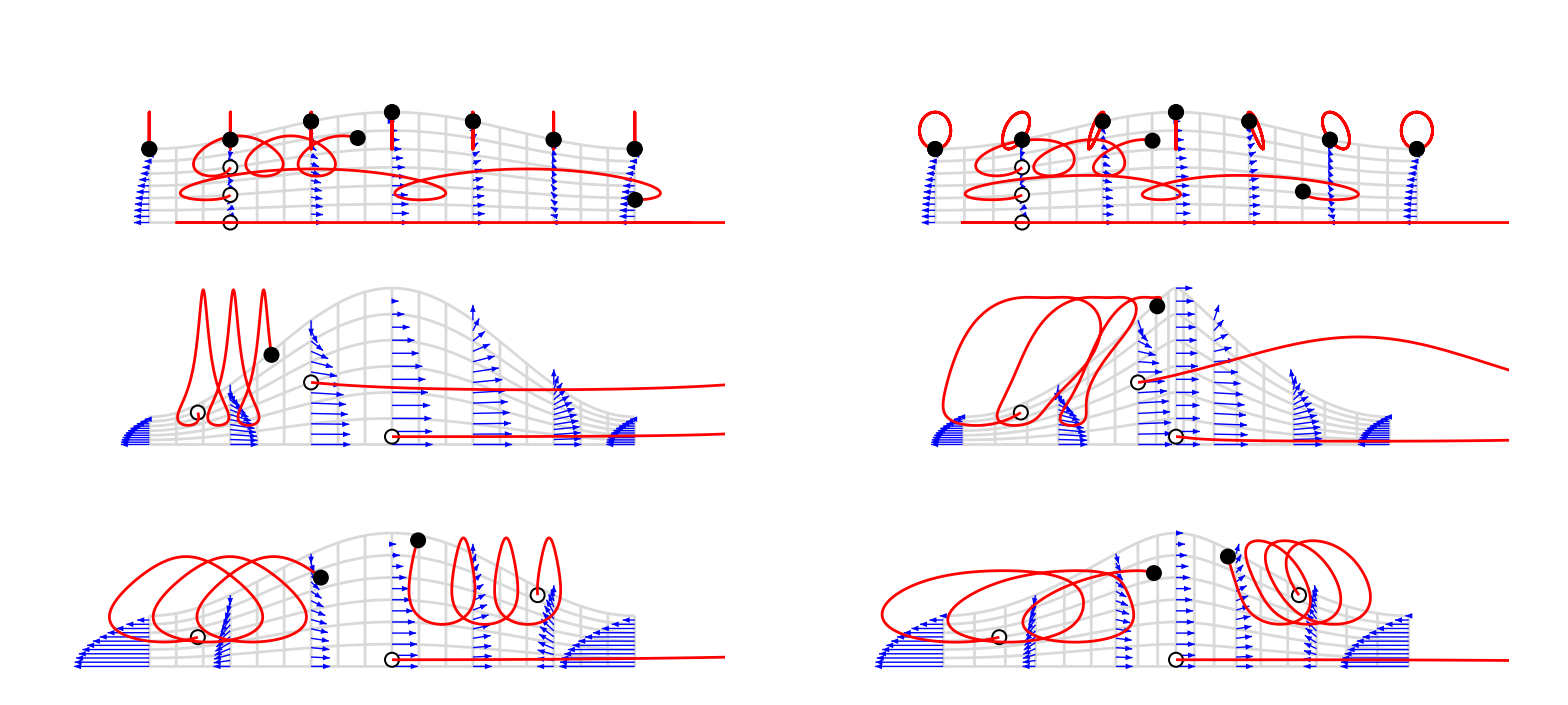

```mathematica
x2 = 3; y2=-.85; w1=3; h1=1;
VgridRadial = Graphics[{
Inset[Vplot1a,{0,0},{Left,Bottom},{w1,h1}],
Inset[Vplot1b,{x2,0},{Left,Bottom},{w1,h1}],
Inset[Vplot2a,{0,y2},{Left,Bottom},{w1,h1}],
Inset[Vplot2b,{x2,y2},{Left,Bottom},{w1,h1}],
Inset[Vplot3a,{0,2y2},{Left,Bottom},{w1,h1}],
Inset[Vplot3b,{x2,2y2},{Left,Bottom},{w1,h1}]},
PlotRange->{{0,6.05},{-1.7,.85}},ImageSize->2400]
```

```mathematica
(* FIGURE 8 *)
```

```mathematica
νa=0; νb=.5;
ΔP1 =0; η1=.2; 
ΔP2 =0; η2=.7;
ΔP3 =1; η3=.45;
t=3; nRGridlines = 6; nXGridlines=18; nRPoints =12; nXPoints = 6; room ={{.16,.16},{.16,1.16}};  
arrowheadSize = 0.01; vMinLength = 1E-10; vMaxLength =0.044; vMaxVal = 1; 
particlePositions1 =  {{-.333,.0},{-.333,.333},{-.333,.667},{-.5,1},{-.333,1},{-.1667,1},{0,1},{.1667,1},{.333,1},{.5,1}};
particlePositions2 ={{0,.05},{-.4,.8},{-.1667,.5}};
particlePositions3 = {{0,.05},{-.4,.5},{.3,.9}};Vplot1a=plotvLongitudinalContractionWaveΩ[t,ΔP1,η1,νa,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions1];
Vplot1b=plotvLongitudinalContractionWaveΩ[t,ΔP1,η1,νb,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions1];
Vplot2a=plotvLongitudinalContractionWaveΩ[t,ΔP2,η2,νa,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions2];
Vplot2b=plotvLongitudinalContractionWaveΩ[t,ΔP2,η2,νb,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions2];
Vplot3a=plotvLongitudinalContractionWaveΩ[t,ΔP3,η3,νa,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions3];
Vplot3b=plotvLongitudinalContractionWaveΩ[t,ΔP3,η3,νb,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions3];
```

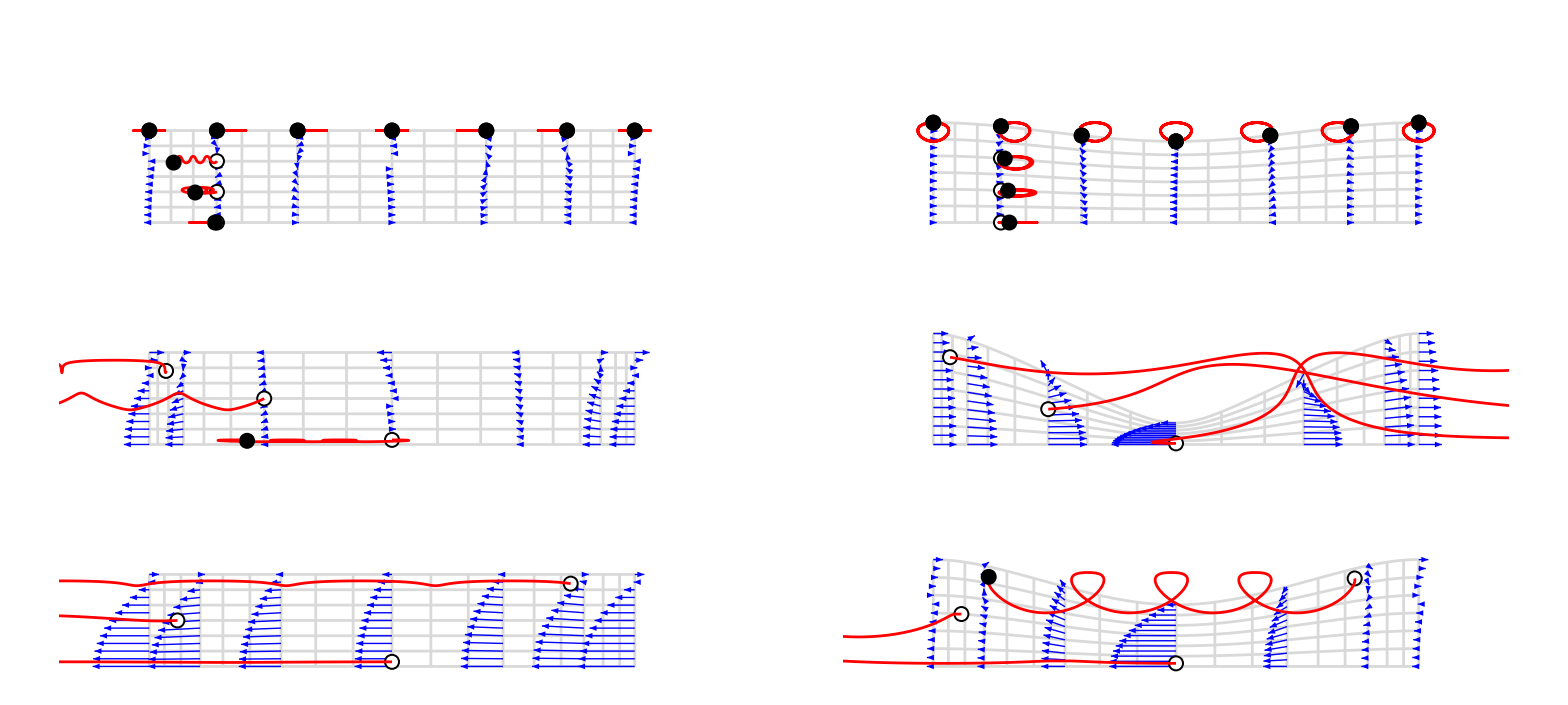

```mathematica
x2 = 3; y2=-.85; w1=3; h1=1;
VgridLongitudinal = Graphics[{
Inset[Vplot1a,{0,0},{Left,Bottom},{w1,h1}],
Inset[Vplot1b,{x2,0},{Left,Bottom},{w1,h1}],
Inset[Vplot2a,{0,y2},{Left,Bottom},{w1,h1}],
Inset[Vplot2b,{x2,y2},{Left,Bottom},{w1,h1}],
Inset[Vplot3a,{0,2y2},{Left,Bottom},{w1,h1}],
Inset[Vplot3b,{x2,2y2},{Left,Bottom},{w1,h1}]},
PlotRange->{{-.001,6.05},{-1.7,.85}},ImageSize->2400]
```

```mathematica
(* FIGURE 2 *)
(* Takes a few minutes to generate. *)
```

```mathematica
ΔP =0; η=.45; ν=.5; 
nRGridlines = 6; nXGridlines=18; 
nRPoints = 12; nXPoints = 6;rm=.5; room ={{rm,rm},{rm,rm}}; 
arrowheadSize = 0.01; vMinLength = arrowheadSize/2; vMaxLength =0.085; vMaxVal = 1; 
particlePositions = {{-.5,1},{-.333,1},{-.1667,1},{0,1},{.1667,1},{.333,1},{.5,1}};
VplotΩ0=plotvRadialContractionWaveΩ[0.0001,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ1=plotvRadialContractionWaveΩ[.25,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ2=plotvRadialContractionWaveΩ[.5,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ3=plotvRadialContractionWaveΩ[.75,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ4=plotvRadialContractionWaveΩ[1,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
```

```mathematica
VplotΩ00=plotvRadialContractionWaveΩ0[0.0001,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ01=plotvRadialContractionWaveΩ0[.25,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ02=plotvRadialContractionWaveΩ0[.5,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ03=plotvRadialContractionWaveΩ0[.75,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ04=plotvRadialContractionWaveΩ0[1,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
```

```mathematica
particlePositions = {{.5,1}};
VplotΩ0Tilde0=plotvRadialContractionWaveΩ0Tilde[0.0001,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ0Tilde1=plotvRadialContractionWaveΩ0Tilde[.25,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ0Tilde2=plotvRadialContractionWaveΩ0Tilde[.5,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ0Tilde3=plotvRadialContractionWaveΩ0Tilde[.75,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
VplotΩ0Tilde4=plotvRadialContractionWaveΩ0Tilde[1,ΔP,η,ν,nRGridlines,nXGridlines,nRPoints,nXPoints,room,vMinLength,vMaxLength,vMaxVal,arrowheadSize,particlePositions];
```

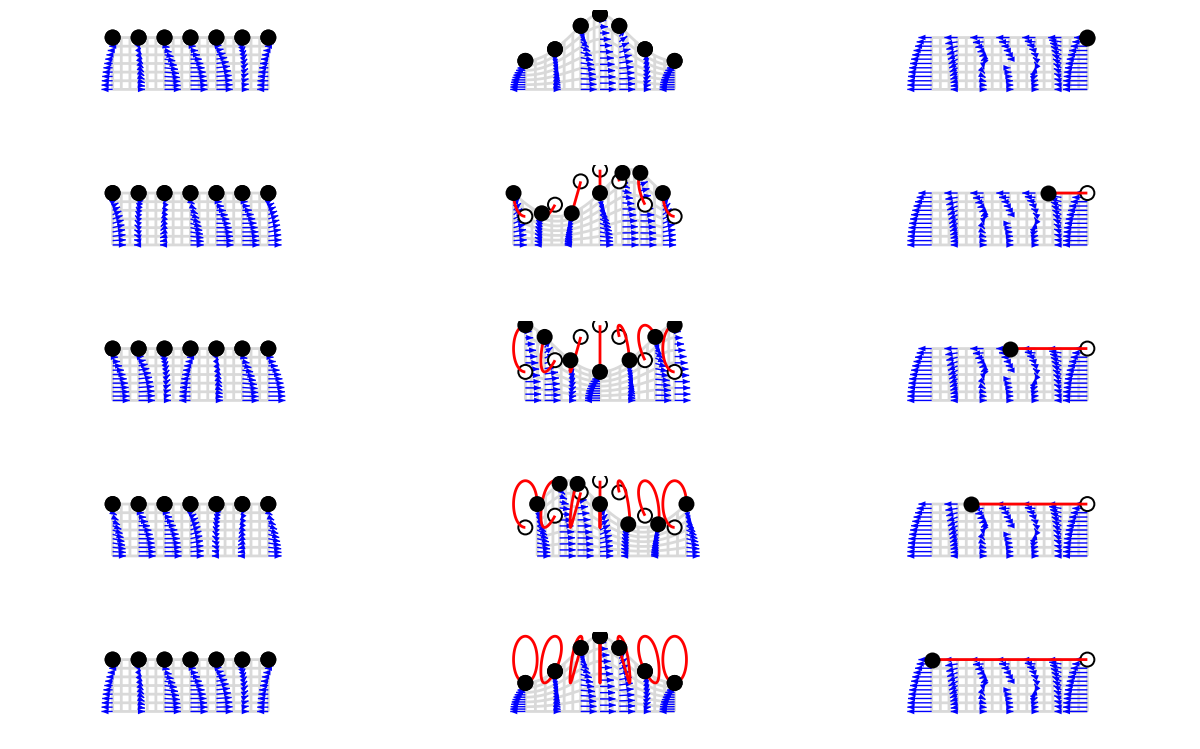

```mathematica
(*Same but with t0.*)
ggrid6=GraphicsGrid[{{VplotΩ00,VplotΩ0,VplotΩ0Tilde0},{VplotΩ01,VplotΩ1,VplotΩ0Tilde1},{VplotΩ02,VplotΩ2,VplotΩ0Tilde2},{VplotΩ03,VplotΩ3,VplotΩ0Tilde3},{VplotΩ04,VplotΩ4,VplotΩ0Tilde4}},ImageSize->1200]
```

```mathematica
(* FIGURE 5 *)
(* Takes a couple minutes to generate. *)
```

```mathematica
νa=0; νb=.5;
ΔP1 =0; η1=.2; 
ΔP2 =0; η2=.7;
ΔP3 =1; η3=.45;
(*Note to self: It's essential in order to make all the plots the same size that there's some space to the left of the sp plot. 
One way to do this is to have a negative value of the ytick, -.2 here. You can delete that later in inkscape.*)
numStreamlines=6; aspectRatioψ = 1/3; aspectRatiosp = 1.5; fs = 32; ticks = {{0,0.5,1},{-.2,0,.5,1}}; pr = {{-.2,1.05},{-.2,1.05}};
Quiet[
ψplot1a=plotψRadialWaveΩ0TildeColored[η1,νa,ΔP1,numStreamlines,aspectRatioψ];
spplot1a = Show[plotspRadialContractionWaveColored[η1,νa,ΔP1],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot1b=plotψRadialWaveΩ0TildeColored[η1,νb,ΔP1,numStreamlines,aspectRatioψ];
spplot1b = Show[plotspRadialContractionWaveColored[η1,νb,ΔP1],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot2a=plotψRadialWaveΩ0TildeColored[η2,νa,ΔP2,numStreamlines,aspectRatioψ];
spplot2a = Show[plotspRadialContractionWaveColored[η2,νa,ΔP2],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot2b=plotψRadialWaveΩ0TildeColored[η2,νb,ΔP2,numStreamlines,aspectRatioψ];
spplot2b = Show[plotspRadialContractionWaveColored[η2,νb,ΔP2],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot3a=plotψRadialWaveΩ0TildeColored[η3,νa,ΔP3,numStreamlines,aspectRatioψ];
spplot3a = Show[plotspRadialContractionWaveColored[η3,νa,ΔP3],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot3b=plotψRadialWaveΩ0TildeColored[η3,νb,ΔP3,numStreamlines,aspectRatioψ];
spplot3b = Show[plotspRadialContractionWaveColored[η3,νb,ΔP3],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
];
```

```mathematica
{calcψExtremaRadialContractionWaveΩ0Tilde[ΔP1,η1,νa][[2]],calcψExtremaRadialContractionWaveΩ0Tilde[ΔP1,η1,νb][[2]]}
{calcψExtremaRadialContractionWaveΩ0Tilde[ΔP2,η2,νa][[2]],calcψExtremaRadialContractionWaveΩ0Tilde[ΔP2,η2,νb][[2]]}
{calcψExtremaRadialContractionWaveΩ0Tilde[ΔP3,η3,νa][[2]],calcψExtremaRadialContractionWaveΩ0Tilde[ΔP3,η3,νb][[2]]}
```

{{-0.869434,0.},{-0.868977,0.}}

{{-0.149914,0.612115},{-0.165639,0.234817}}

{{-0.835255,0.0368152},{-0.81019,0.}}

```mathematica
(*Format: Inset[plot,{xpos,ypos},{relative to what},{width,height}]. Keep height=1 to fix aspect ratio.*)
```

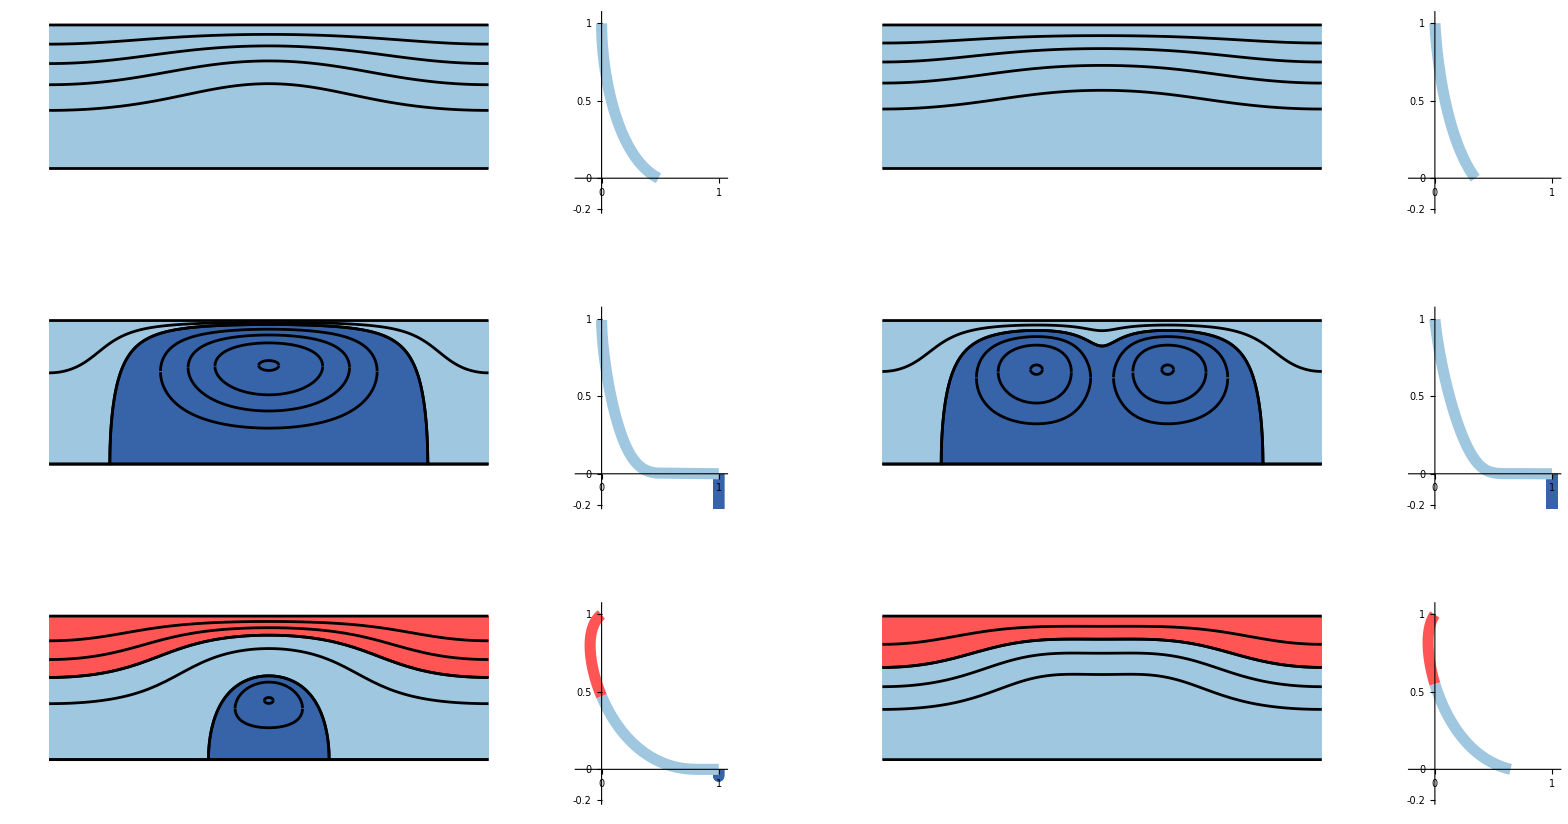

```mathematica
x1=3.1; x2 = 4.65; x3=x1+x2; y1=-.26; y2=-1.65; w1=3; h1=1; w2=1; h2=1.3;
ψgridRadial2 = Graphics[{
Inset[ψplot1a,{0,0},{Left,Bottom},{w1,h1}],
Inset[spplot1a,{x1,y1},{Left,Bottom},{w2,h2}],
Inset[ψplot1b,{x2,0},{Left,Bottom},{w1,h1}],
Inset[spplot1b,{x1+x2,y1},{Left,Bottom},{w2,h2}],
Inset[ψplot2a,{0,y2},{Left,Bottom},{w1,h1}],
Inset[spplot2a,{x1,y2+y1},{Left,Bottom},{w2,h2}],
Inset[ψplot2b,{x2,y2},{Left,Bottom},{w1,h1}],
Inset[spplot2b,{x1+x2,y2+y1},{Left,Bottom},{w2,h2}],
Inset[ψplot3a,{0,2y2},{Left,Bottom},{w1,h1}],
Inset[spplot3a,{x1,2y2+y1},{Left,Bottom},{w2,h2}],
Inset[ψplot3b,{x2,2y2},{Left,Bottom},{w1,h1}],
Inset[spplot3b,{x1+x2,2y2+y1},{Left,Bottom},{w2,h2}]},
PlotRange->{{0,8.8},{-3.6,1.15}},ImageSize->2400]
```

```mathematica
(* FIGURE 9 *)
(* Takes a couple minutes to generate. *)
```

```mathematica
νa=0; νb=.5;
ΔP1 =0; η1=.2; 
ΔP2 =0; η2=.7;
ΔP3 =1; η3=.45;
(*Note to self: It's essential in order to make all the plots the same size that there's some space to the left of the sp plot. 
One way to do this is to have a negative value of the ytick, -.2 here. You can delete that later in inkscape.*)
numStreamlines=6; aspectRatioψ = 1/3; aspectRatiosp = 1.5; fs = 32; ticks = {{0,0.5,1},{-.2,0,.5,1}}; pr = {{-.5,1.05},{-.2,1.05}};
Quiet[
ψplot1a=plotψLongitudinalWaveΩ0TildeColored[η1,νa,ΔP1,numStreamlines,aspectRatioψ];
spplot1a = Show[plotspLongitudinalContractionWaveColored[η1,νa,ΔP1],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot1b=plotψLongitudinalWaveΩ0TildeColored[η1,νb,ΔP1,numStreamlines,aspectRatioψ];
spplot1b = Show[plotspLongitudinalContractionWaveColored[η1,νb,ΔP1],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot2a=plotψLongitudinalWaveΩ0TildeColored[η2,νa,ΔP2,numStreamlines,aspectRatioψ];
spplot2a = Show[plotspLongitudinalContractionWaveColored[η2,νa,ΔP2],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot2b=plotψLongitudinalWaveΩ0TildeColored[η2,νb,ΔP2,numStreamlines,aspectRatioψ];
spplot2b = Show[plotspLongitudinalContractionWaveColored[η2,νb,ΔP2],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot3a=plotψLongitudinalWaveΩ0TildeColored[η3,νa,ΔP3,numStreamlines,aspectRatioψ];
spplot3a = Show[plotspLongitudinalContractionWaveColored[η3,νa,ΔP3],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
ψplot3b=plotψLongitudinalWaveΩ0TildeColored[η3,νb,ΔP3,numStreamlines,aspectRatioψ];
spplot3b = Show[plotspLongitudinalContractionWaveColored[η3,νb,ΔP3],PlotRange->pr,AxesLabel->None,AspectRatio->aspectRatiosp,BaseStyle->fs,Ticks->ticks];
];
```

```mathematica
{calcψExtremaLongitudinalContractionWaveΩ0Tilde[ΔP1,η1,νa][[2]],calcψExtremaLongitudinalContractionWaveΩ0Tilde[ΔP1,η1,νb][[2]]}
{calcψExtremaLongitudinalContractionWaveΩ0Tilde[ΔP2,η2,νa][[2]],calcψExtremaLongitudinalContractionWaveΩ0Tilde[ΔP2,η2,νb][[2]]}
{calcψExtremaLongitudinalContractionWaveΩ0Tilde[ΔP3,η3,νa][[2]],calcψExtremaLongitudinalContractionWaveΩ0Tilde[ΔP3,η3,νb][[2]]}
```

{{-1.02,0.},{-0.967288,0.}}

{{-1.245,0.},{-0.157136,0.139472}}

{{-2.10125,0.},{-1.24945,0.}}

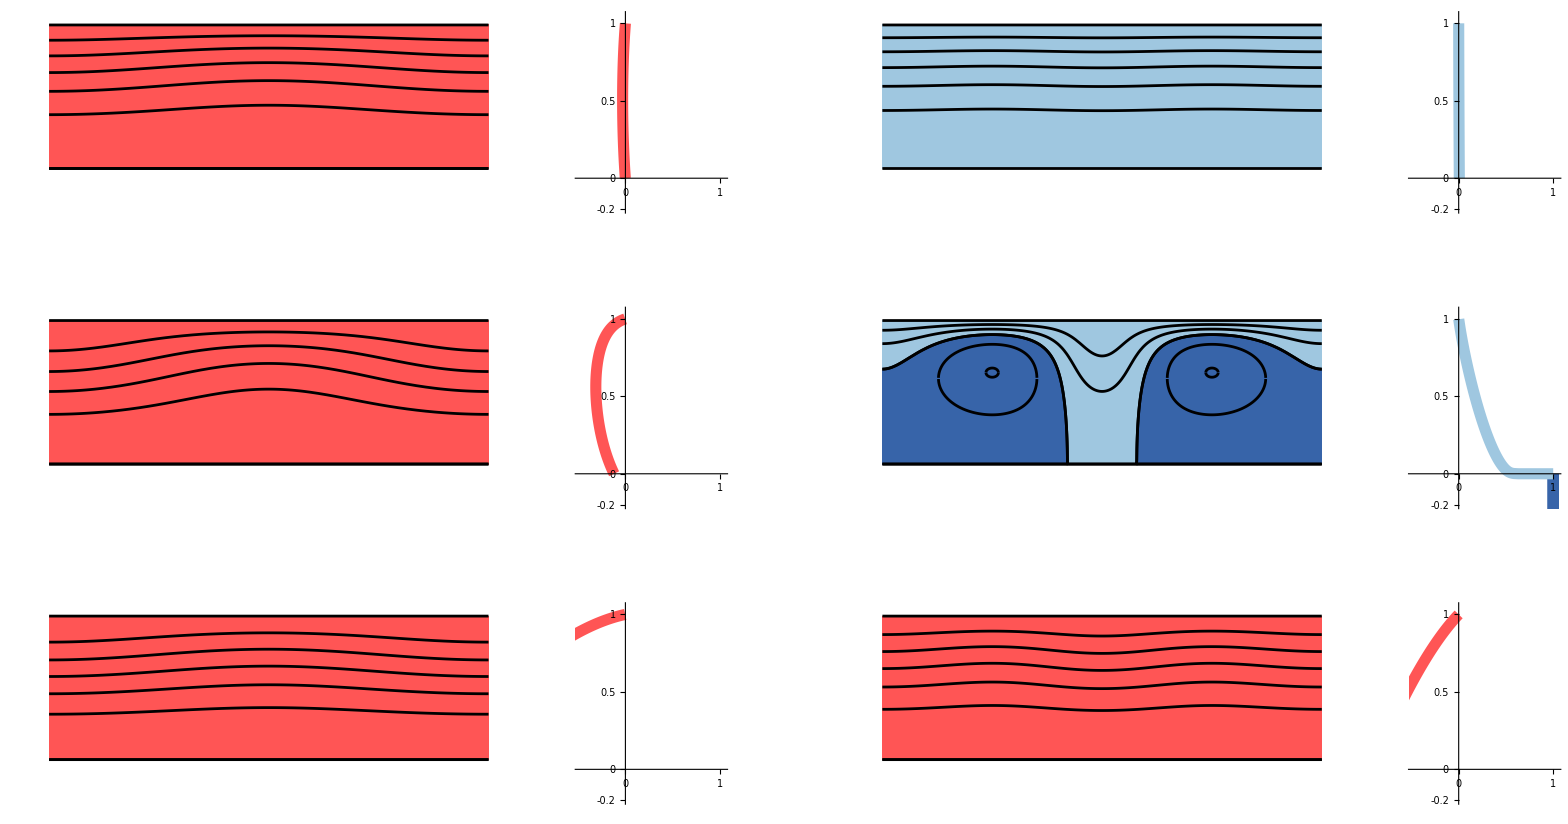

```mathematica
x1=3.1; x2 = 4.65; x3=x1+x2; y1=-.26; y2=-1.65; w1=3; h1=1; w2=1; h2=1.3;
ψgridLongitudinal2 = Graphics[{
Inset[ψplot1a,{0,0},{Left,Bottom},{w1,h1}],
Inset[spplot1a,{x1,y1},{Left,Bottom},{w2,h2}],
Inset[ψplot1b,{x2,0},{Left,Bottom},{w1,h1}],
Inset[spplot1b,{x1+x2,y1},{Left,Bottom},{w2,h2}],
Inset[ψplot2a,{0,y2},{Left,Bottom},{w1,h1}],
Inset[spplot2a,{x1,y2+y1},{Left,Bottom},{w2,h2}],
Inset[ψplot2b,{x2,y2},{Left,Bottom},{w1,h1}],
Inset[spplot2b,{x1+x2,y2+y1},{Left,Bottom},{w2,h2}],
Inset[ψplot3a,{0,2y2},{Left,Bottom},{w1,h1}],
Inset[spplot3a,{x1,2y2+y1},{Left,Bottom},{w2,h2}],
Inset[ψplot3b,{x2,2y2},{Left,Bottom},{w1,h1}],
Inset[spplot3b,{x1+x2,2y2+y1},{Left,Bottom},{w2,h2}]},
PlotRange->{{0,8.8},{-3.6,1.15}},ImageSize->2400]
```